```mathematica
(*Порог ошибки*)
ϵ=0.1;
(*Доверительный уровень*)
δ=0.05;
(*Вводим данные, согласно условию*)
(*Невозрастающая последовательность собственных чисел ковариационного оператора*)
λ[k_]:=1/(π^2 k^2);
(*Соотвтетствующие собственным числам собственные функции*)
(*Subscript[Κψ, k]=Subscript[λ, k] Subscript[ψ, k]  k=1,2,...*)
ψ[k_, t_]:=√2 Cos[π k t];
```

```mathematica
(*Алгоритм вычисления сложности аппроксимации по вероятности n^prob(ϵ,δ)*)
(*Количество выборок случайных величин*)
NS=100;
(*Объем каждой выборки*)
NCS=300;
(*Задаем матрицу случайных величин - выборки*)
(*Случайные величины в строке приналежат к одной выборке*)
MS=Table[RandomVariate[NormalDistribution[0,1]],{i,1,NCS} ,{j,1,NS}];
(*Задем след ковариационного оператора*)
Λ=∑_(k=1)^(+∞) λ[k];
Print["ϵ^2*Λ = ", ϵ^2*Λ]
```

ϵ^2*Λ = 0.00166667

```mathematica
(*Начальное значение вероятности равно 1*)
P=1;
(*Задаем начальное значение для n*)
n=0;
(*Пока вероятность больше заданой доверительной ошибки*)
While[P>δ,
(*Количество успехов*)
SC=0;
(*Цикл по всем выборкам*)
For[i=1, i≤NS,  i++,
(*Если условие выполено, то увеличиваем количество успехов*)
If[∑_(k=n+1)^NCS λ[k]*(MS[[k,i]])^2>  ϵ^2*Λ,SC=SC+1; ]
 ];(*Конец цикла по выборкам*)
(*Увеличиваем n*)
n=n+1;
(*Считаем вероятность P = (количество успехов)/(количество выборок)*)
P=SC/NS;
]; (*Конец цикла пока*)
Print["n = ", n]
Print["P = ", N[P]]
```

n = 61

P = 0.03

При n = 61

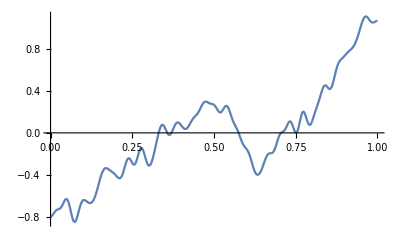

```mathematica
(*Для разбиения отрезка [0,1] на равные интервалы*)
maxt=10000;
(*Генерируем последовательность n случайных величин распределенных по нормальному закону*)
ξ=RandomVariate[NormalDistribution[0,1],n];
(*Разложение Кархунена-Лоэва для заданного гауссовского процесса W^C(t)=W(t)-∫_0^1 W(s)ⅆs*)
W[t_]=∑_(k=1)^n √λ[k]*ψ[k, t]*ξ[[k]];
Print["При n = ",n];
(*Составляем таблицу значений функции с шагом t в 1/maxt*)
Print[ListLinePlot[Table[{s/maxt,W[s/maxt]},{s,0,maxt}]]];
```